```mathematica
Clear["Global`*"];
Off[NIntegrate::ncvb];
```

```mathematica
BasisFunction[n_]:=Function[{x},LegendreP[n,x]];
BasisMax=30;
BasisFunctionNorm=Table[NIntegrate[(BasisFunction[n][x])^2,{x,-1,1}]×0+2/(2n+1),{n,0,BasisMax}];
qFunction[x_]=PDF[NormalDistribution[0.1,0.2],x];
Plot[Evaluate[Table[BasisFunction[n][x],{n,0,BasisMax}]],{x,-1,1},ImageSize->Medium];
```

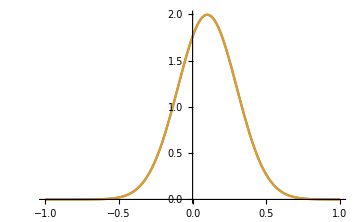

```mathematica
c=Table[NIntegrate[BasisFunction[n][x]×qFunction[x],{x,-1,1}]/BasisFunctionNorm[[n+1]],{n,0,BasisMax}];
Plot[Evaluate[{qFunction[x],Sum[c[[n+1]]×BasisFunction[n][x],{n,0,BasisMax}]}],{x,-1,1},ImageSize->Medium]
```

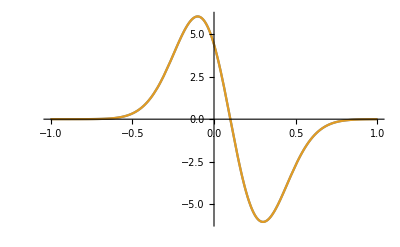

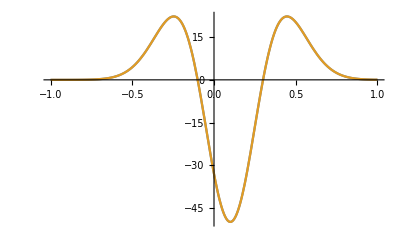

```mathematica
(DevariateMatrix=Sum[DiagonalMatrix[Table[2i+1,{i,0,BasisMax-1}][[;;BasisMax-(i-1)]],i],{i,1,BasisMax,2}])//MatrixForm;
Plot[Evaluate[{D[qFunction[x], x],Sum[(DevariateMatrix.c)[[n+1]]×BasisFunction[n][x],{n,0,BasisMax}]}],{x,-1,1}]
(DevariateMatrix2=DevariateMatrix.DevariateMatrix)//MatrixForm;
Plot[Evaluate[{D[qFunction[x], x,x],Sum[(DevariateMatrix2.c)[[n+1]]×BasisFunction[n][x],{n,0,BasisMax}]}],{x,-1,1}]
```

```mathematica
cInverse=Inverse[DevariateMatrix2[[;;-3,3;;]]].c[[;;-3]];
a=Sum[cInverse[[i-1]]×BasisFunction[i][-1],{i,2,BasisMax}];
b=Sum[cInverse[[i-1]]×BasisFunction[i][+1],{i,2,BasisMax}];
AddOn={-(a+b)/2,-(b-a)/2};
cInverseFull=AddOn~Join~cInverse;
```

```mathematica
ϕLeft=0;
ϕRight=0;
AnaliticalSolve=DSolve[{D[ϕ[x], x,x]== qFunction[x],ϕ[-1]==ϕLeft,ϕ[1]==ϕRight},ϕ[x],{x,-1,1}][[1,1]];
```

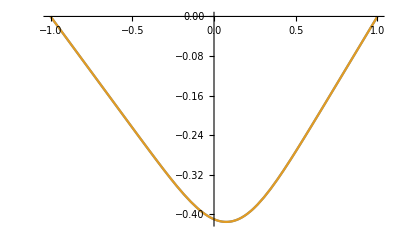

```mathematica
Plot[Evaluate[{
ϕ[x]/.AnaliticalSolve,
Sum[cInverseFull[[n+1]]×BasisFunction[n][x],{n,0,BasisMax}]
}],{x,-1,1}]
```